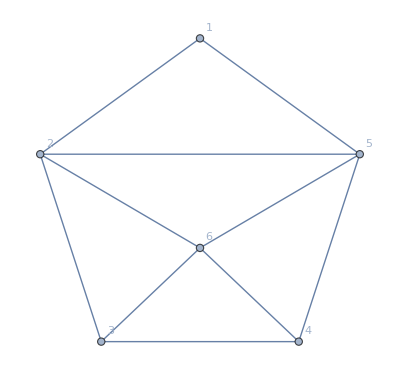

```mathematica
full=Graph[{1<->2,2<->3,3<->4,4<->5,5<->1,2<->5,2<->6,3<->6,4<->6,5<->6},VertexLabels->"Name",GraphLayout->"TutteEmbedding"]
```

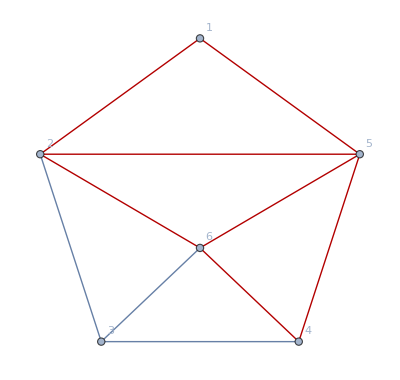
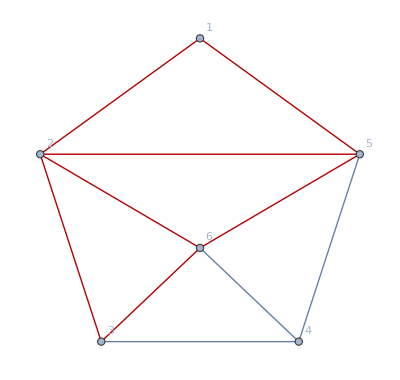

```mathematica
Table[Graph[{1<->2,2<->3,3<->4,4<->5,5<->1,2<->5,2<->6,3<->6,4<->6,5<->6},VertexLabels->"Name",GraphLayout->"TutteEmbedding",GraphHighlight->EdgeList[VertexDelete[full,k]]],
{k,{3,4}}]
```

```mathematica
Graph[{1<->2,2<->3,3<->4,4<->5,5<->1,2<->5,2<->6,3<->6,4<->6,5<->6},VertexLabels->"Name",GraphLayout->"TutteEmbedding",GraphHighlight->{1<->2,2<->3,3<->4,4<->5,5<->1,2<->5,2<->6,3<->6,4<->6,5<->6}]
```

```mathematica
allGraphs5[amigo1,"children"]
```

{{29494,29602},{29440,29551},{29416,29446}}

```mathematica
Select[Keys[allGraphs6],Sort[Map[Sort,EdgeList[allGraphs6[#,"graph"]]]]==Sort[Map[Sort,EdgeList[full]]]&]
```

{4982998}

```mathematica
ShowGraph6Least[4982998]
```

-Graphics-4982998GreaterEqual

```mathematica
allGraphs6[4982998,"colofour"]/.RepGraph6["C"]
```

-Graphics-7240144+-Graphics-8775337+-Graphics-7240063+-Graphics-7705975+-Graphics-7181095+-Graphics-7233583+-Graphics-8768776+-Graphics-7705894+-Graphics-7181014+-Graphics-7233502+-Graphics-7174534+-Graphics-7174453

```mathematica
greq=Select[Keys[allGraphs6],allGraphs6[#,"comp"]===GreaterEqual&];Length[greq]
```

13512

```mathematica
MyPlanar6[key_]:=Block[
{item=allGraphs6[key], emb, pos=Association[],posOuter=Association[], length,lines={},sets,res,line1,line2,crit, found=False,mat,i,j,x,y, challenge},
x=Symbol["abcx"<>ToString[key]];
y=Symbol["abcy"<>ToString[key]];
emb=GraphEmbedding[item["graph"]];
length=Length[Flatten[item["vertexsets"]]]-1;
mat=item["matrix"];
i=1;
Table[
Table[
pos[v]=IntegerPart[100*Round[emb[[i]],0.01]];
,{v,Select[set,#≠6&]}
];
i++
,{set,item["vertexsets"]}
];
Table[posOuter[k]=200*{Cos[(2π/length )(length-k+1)+Pi/2],Sin[(2π/length )(k-1)+Pi/2]},{k,length}];
Table[crit=MakeLineSegmentCrit[pos[k],posOuter[k], "Node is outward connected " <> ToString[k],x,y];lines=Append[ lines,crit],{k,length}];

Table[
i=Min[item["vertexsets"][[e[[1]]]]];
j=Min[item["vertexsets"][[e[[2]]]]];
If[i≠6&&j≠6,
crit=MakeLineSegmentCrit[pos[i],pos[j], "Connection between node " <> ToString[i<->j],x,y ];lines=Append[ lines,crit]
],
{e,EdgeList[item["graph"]]}
];
(*PrintTemporary["line segments computed : " ,Length[lines]];*)
sets=Subsets[Range[Length[lines]],{2}];
Table[
line1=lines[[s[[1]]]];
line2=lines[[s[[2]]]];
Quiet[
challenge=line1["crit"]&&line2["crit"];
res=NSolve[line1["crit"]&&line2["crit"],{x,y}];
];
If[res≠{},(*Print[key ,": Not planar because of ",s,stubbornForm6[key,"graph"], line1["what"],"  ",line1["crit"], "    ", line2["what"],"   ",  line2["crit"],  "     ", res];*)found=True;Return[True]];
,{s,sets}
];
!found
]
```

```mathematica
MyPlanar6[4982998]
```

True

```mathematica
greq2=Select[Take[greq,50],MyPlanar6[#]&];Print[Length[greq2]]
```

1

```mathematica
greq2
```

{7174786}

```mathematica
Table[ShowGraph6Least[k],{k,greq2}]
```

{-Graphics-7174786GreaterEqual}

```mathematica
greq2=Monitor[Table[MyPlanar6[greq[[k]]],{k,Length[greq]}],Row[{k,ProgressIndicator[k/Length[greq]],Length[greq]}]]
```

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,13422,True,True,True,True,True,True,False,False,False,True,True,True,False,False,False,True,True,True,False,True,True,True,True,True,True,False,False,False,False,False,False,False,False,True,True,True,True,True,True,True,True,True,True,True,True}
 |  |  |  |

```mathematica
Tally[greq2]
```

{{False,10946},{True,2566}}

```mathematica
greq3=Select[Table[If[greq2[[k]],greq[[k]],0],{k,Length[greq]}],#≠0&];
```

```mathematica
Length[greq3]
```

2566

```mathematica
Table[ShowGraph6Least[k],{k,Select[greq3,MemberQ[allGraphs5AtomKeys,#]&]}]
```

{-Graphics-29533GreaterEqual,-Graphics-29560GreaterEqual,-Graphics-29767GreaterEqual,-Graphics-29797GreaterEqual,-Graphics-31711GreaterEqual,-Graphics-31714GreaterEqual,-Graphics-31738GreaterEqual,-Graphics-31954GreaterEqual,-Graphics-31984GreaterEqual,-Graphics-38281GreaterEqual,-Graphics-38308GreaterEqual,-Graphics-49207GreaterEqual,-Graphics-49210GreaterEqual,-Graphics-51475GreaterEqual,-Graphics-51478GreaterEqual}

```mathematica
Tally[Table[allGraphs6[k,"comp"],{k,allGraphs6AtomKeys}]]
```

{{Equal,16},{GreaterEqual,151},{Greater,36}}

```mathematica
Tally[Table[allGraphs6[k,"comp"],{k,Keys[allGraphs6]}]]
```

{{Greater,39372},{GreaterEqual,13512},{Equal,187}}